# Assignment 10 - Cameron Embree

4/4/14 - Due April 7, Allie also worked with me

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets the directory to look for files to the same directory the notebook (this file) is in*)
rawdata=Import["Constitutional_Convention_Votes.csv"];
(*votecodes 1 -> Yea, 0 -> Nay, 6-> Abstain*)
```

```mathematica
statePostCode=Table[rawdata[[i,1]],{i,1,rawdata//Length}]
Print["There are ",rawdata//Length," voters"]
```

{NH,MA,CT,NY,NJ,PA,DE,MD,VA,NC,SC,GA}

There are 12 voters

```mathematica
psim[i_,j_]:=Module[{},
combinedTotNonAbstained=Flatten[Join[
Position[rawdata[[i,All]],0],Position[rawdata[[i,All]],1],
Position[rawdata[[j,All]],0],Position[rawdata[[j,All]],1]]]//Tally;
same=Select[combinedTotNonAbstained,#[[2]]>1&];
Length[same]/Length[combinedTotNonAbstained]//N
]


datSize=rawdata//Length;
A=Table[psim[i,j],{i,1,datSize},{j,1,datSize}];
Print["Relationship between voters:",A//MatrixForm]
```

{{1.,0.636971,0.556277,0.618629,0.572632,0.592751,0.557895,0.543788,0.554415,0.578838,0.600877,0.591966},{0.636971,1.,0.510689,0.540441,0.492135,0.56974,0.5,0.473799,0.549425,0.595294,0.578049,0.576471},{0.556277,0.510689,1.,0.516605,0.528302,0.496536,0.48037,0.525463,0.481982,0.497738,0.484706,0.513889},{0.618629,0.540441,0.516605,1.,0.588785,0.559633,0.561111,0.582721,0.577982,0.597043,0.53407,0.585185},{0.572632,0.492135,0.528302,0.588785,1.,0.495575,0.545035,0.526667,0.462687,0.471215,0.448352,0.542986},{0.592751,0.56974,0.496536,0.559633,0.495575,1.,0.552204,0.526667,0.633333,0.516484,0.49095,0.512195},{0.557895,0.5,0.48037,0.561111,0.545035,0.552204,1.,0.574074,0.485777,0.465665,0.432967,0.461039},{0.543788,0.473799,0.525463,0.582721,0.526667,0.526667,0.574074,1.,0.559284,0.49467,0.447084,0.519737},{0.554415,0.549425,0.481982,0.577982,0.462687,0.633333,0.485777,0.559284,1.,0.598174,0.510158,0.57631},{0.578838,0.595294,0.497738,0.597043,0.471215,0.516484,0.465665,0.49467,0.598174,1.,0.57243,0.60739},{0.600877,0.578049,0.484706,0.53407,0.448352,0.49095,0.432967,0.447084,0.510158,0.57243,1.,0.654229},{0.591966,0.576471,0.513889,0.585185,0.542986,0.512195,0.461039,0.519737,0.57631,0.60739,0.654229,1.}}

The relationship between the voters:(1. | 0.636971 | 0.556277 | 0.618629 | 0.572632 | 0.592751 | 0.557895 | 0.543788 | 0.554415 | 0.578838 | 0.600877 | 0.591966
0.636971 | 1. | 0.510689 | 0.540441 | 0.492135 | 0.56974 | 0.5 | 0.473799 | 0.549425 | 0.595294 | 0.578049 | 0.576471
0.556277 | 0.510689 | 1. | 0.516605 | 0.528302 | 0.496536 | 0.48037 | 0.525463 | 0.481982 | 0.497738 | 0.484706 | 0.513889
0.618629 | 0.540441 | 0.516605 | 1. | 0.588785 | 0.559633 | 0.561111 | 0.582721 | 0.577982 | 0.597043 | 0.53407 | 0.585185
0.572632 | 0.492135 | 0.528302 | 0.588785 | 1. | 0.495575 | 0.545035 | 0.526667 | 0.462687 | 0.471215 | 0.448352 | 0.542986
0.592751 | 0.56974 | 0.496536 | 0.559633 | 0.495575 | 1. | 0.552204 | 0.526667 | 0.633333 | 0.516484 | 0.49095 | 0.512195
0.557895 | 0.5 | 0.48037 | 0.561111 | 0.545035 | 0.552204 | 1. | 0.574074 | 0.485777 | 0.465665 | 0.432967 | 0.461039
0.543788 | 0.473799 | 0.525463 | 0.582721 | 0.526667 | 0.526667 | 0.574074 | 1. | 0.559284 | 0.49467 | 0.447084 | 0.519737
0.554415 | 0.549425 | 0.481982 | 0.577982 | 0.462687 | 0.633333 | 0.485777 | 0.559284 | 1. | 0.598174 | 0.510158 | 0.57631
0.578838 | 0.595294 | 0.497738 | 0.597043 | 0.471215 | 0.516484 | 0.465665 | 0.49467 | 0.598174 | 1. | 0.57243 | 0.60739
0.600877 | 0.578049 | 0.484706 | 0.53407 | 0.448352 | 0.49095 | 0.432967 | 0.447084 | 0.510158 | 0.57243 | 1. | 0.654229
0.591966 | 0.576471 | 0.513889 | 0.585185 | 0.542986 | 0.512195 | 0.461039 | 0.519737 | 0.57631 | 0.60739 | 0.654229 | 1.)

12.+(0.636971-√((x[1,1]-x[2,1])^2))^2+(0.556277-√((x[1,1]-x[3,1])^2))^2+(0.510689-√((x[2,1]-x[3,1])^2))^2+(0.618629-√((x[1,1]-x[4,1])^2))^2+(0.540441-√((x[2,1]-x[4,1])^2))^2+(0.516605-√((x[3,1]-x[4,1])^2))^2+(0.572632-√((x[1,1]-x[5,1])^2))^2+(0.492135-√((x[2,1]-x[5,1])^2))^2+(0.528302-√((x[3,1]-x[5,1])^2))^2+(0.588785-√((x[4,1]-x[5,1])^2))^2+(0.592751-√((x[1,1]-x[6,1])^2))^2+(0.56974-√((x[2,1]-x[6,1])^2))^2+(0.496536-√((x[3,1]-x[6,1])^2))^2+(0.559633-√((x[4,1]-x[6,1])^2))^2+(0.495575-√((x[5,1]-x[6,1])^2))^2+(0.557895-√((x[1,1]-x[7,1])^2))^2+(0.5-√((x[2,1]-x[7,1])^2))^2+(0.48037-√((x[3,1]-x[7,1])^2))^2+(0.561111-√((x[4,1]-x[7,1])^2))^2+(0.545035-√((x[5,1]-x[7,1])^2))^2+(0.552204-√((x[6,1]-x[7,1])^2))^2+(0.543788-√((x[1,1]-x[8,1])^2))^2+(0.473799-√((x[2,1]-x[8,1])^2))^2+(0.525463-√((x[3,1]-x[8,1])^2))^2+(0.582721-√((x[4,1]-x[8,1])^2))^2+(0.526667-√((x[5,1]-x[8,1])^2))^2+(0.526667-√((x[6,1]-x[8,1])^2))^2+(0.574074-√((x[7,1]-x[8,1])^2))^2+(0.554415-√((x[1,1]-x[9,1])^2))^2+(0.549425-√((x[2,1]-x[9,1])^2))^2+(0.481982-√((x[3,1]-x[9,1])^2))^2+(0.577982-√((x[4,1]-x[9,1])^2))^2+(0.462687-√((x[5,1]-x[9,1])^2))^2+(0.633333-√((x[6,1]-x[9,1])^2))^2+(0.485777-√((x[7,1]-x[9,1])^2))^2+(0.559284-√((x[8,1]-x[9,1])^2))^2+(0.578838-√((x[1,1]-x[10,1])^2))^2+(0.595294-√((x[2,1]-x[10,1])^2))^2+(0.497738-√((x[3,1]-x[10,1])^2))^2+(0.597043-√((x[4,1]-x[10,1])^2))^2+(0.471215-√((x[5,1]-x[10,1])^2))^2+(0.516484-√((x[6,1]-x[10,1])^2))^2+(0.465665-√((x[7,1]-x[10,1])^2))^2+(0.49467-√((x[8,1]-x[10,1])^2))^2+(0.598174-√((x[9,1]-x[10,1])^2))^2+(0.600877-√((x[1,1]-x[11,1])^2))^2+(0.578049-√((x[2,1]-x[11,1])^2))^2+(0.484706-√((x[3,1]-x[11,1])^2))^2+(0.53407-√((x[4,1]-x[11,1])^2))^2+(0.448352-√((x[5,1]-x[11,1])^2))^2+(0.49095-√((x[6,1]-x[11,1])^2))^2+(0.432967-√((x[7,1]-x[11,1])^2))^2+(0.447084-√((x[8,1]-x[11,1])^2))^2+(0.510158-√((x[9,1]-x[11,1])^2))^2+(0.57243-√((x[10,1]-x[11,1])^2))^2+(0.591966-√((x[1,1]-x[12,1])^2))^2+(0.576471-√((x[2,1]-x[12,1])^2))^2+(0.513889-√((x[3,1]-x[12,1])^2))^2+(0.585185-√((x[4,1]-x[12,1])^2))^2+(0.542986-√((x[5,1]-x[12,1])^2))^2+(0.512195-√((x[6,1]-x[12,1])^2))^2+(0.461039-√((x[7,1]-x[12,1])^2))^2+(0.519737-√((x[8,1]-x[12,1])^2))^2+(0.57631-√((x[9,1]-x[12,1])^2))^2+(0.60739-√((x[10,1]-x[12,1])^2))^2+(0.654229-√((x[11,1]-x[12,1])^2))^2

{17.1503,{x[1,1]→0.590587,x[2,1]→0.0939658,x[3,1]→-0.0729697,x[4,1]→0.377448,x[5,1]→0.434259,x[6,1]→0.172124,x[7,1]→-0.161048,x[8,1]→-0.255262,x[9,1]→0.290113,x[10,1]→-0.341513,x[11,1]→0.00924673,x[12,1]→-0.45495,x[13,1]→0.505822}}

{x[1,1],x[2,1],x[3,1],x[4,1],x[5,1],x[6,1],x[7,1],x[8,1],x[9,1],x[10,1],x[11,1],x[12,1],x[13,1]}

{{0.590587},{0.0939658},{-0.0729697},{0.377448},{0.434259},{0.172124},{-0.161048},{-0.255262},{0.290113},{-0.341513},{0.00924673},{-0.45495}}

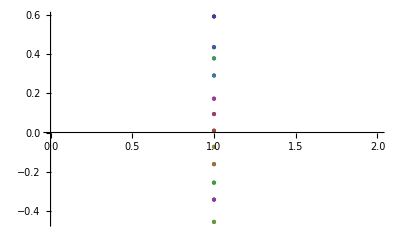

```mathematica
(*stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
*)
n=datSize; (*12*)
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,13},{j,1}]]]

Flatten[Table[x[i,j],{i,13},{j,1}]]

(*Print["W/O: ",p=mds[[2,All,-1]]]
Print["PAR: ",p=Partition[mds[[2,All,-1]],1]]*)
p=Partition[mds[[2,All,-1]],1];
a=Table[Tooltip[p[[i]],statePostCode[[i]]],{i,1,statePostCode//Length}]

ListPlot[a,Mesh->All]
```

12.+(0.636971-√((x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2))^2+(0.556277-√((x[1,1]-x[3,1])^2+(x[1,2]-x[3,2])^2))^2+(0.510689-√((x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2))^2+(0.618629-√((x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2))^2+(0.540441-√((x[2,1]-x[4,1])^2+(x[2,2]-x[4,2])^2))^2+(0.516605-√((x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2))^2+(0.572632-√((x[1,1]-x[5,1])^2+(x[1,2]-x[5,2])^2))^2+(0.492135-√((x[2,1]-x[5,1])^2+(x[2,2]-x[5,2])^2))^2+(0.528302-√((x[3,1]-x[5,1])^2+(x[3,2]-x[5,2])^2))^2+(0.588785-√((x[4,1]-x[5,1])^2+(x[4,2]-x[5,2])^2))^2+(0.592751-√((x[1,1]-x[6,1])^2+(x[1,2]-x[6,2])^2))^2+(0.56974-√((x[2,1]-x[6,1])^2+(x[2,2]-x[6,2])^2))^2+(0.496536-√((x[3,1]-x[6,1])^2+(x[3,2]-x[6,2])^2))^2+(0.559633-√((x[4,1]-x[6,1])^2+(x[4,2]-x[6,2])^2))^2+(0.495575-√((x[5,1]-x[6,1])^2+(x[5,2]-x[6,2])^2))^2+(0.557895-√((x[1,1]-x[7,1])^2+(x[1,2]-x[7,2])^2))^2+(0.5-√((x[2,1]-x[7,1])^2+(x[2,2]-x[7,2])^2))^2+(0.48037-√((x[3,1]-x[7,1])^2+(x[3,2]-x[7,2])^2))^2+(0.561111-√((x[4,1]-x[7,1])^2+(x[4,2]-x[7,2])^2))^2+(0.545035-√((x[5,1]-x[7,1])^2+(x[5,2]-x[7,2])^2))^2+(0.552204-√((x[6,1]-x[7,1])^2+(x[6,2]-x[7,2])^2))^2+(0.543788-√((x[1,1]-x[8,1])^2+(x[1,2]-x[8,2])^2))^2+(0.473799-√((x[2,1]-x[8,1])^2+(x[2,2]-x[8,2])^2))^2+(0.525463-√((x[3,1]-x[8,1])^2+(x[3,2]-x[8,2])^2))^2+(0.582721-√((x[4,1]-x[8,1])^2+(x[4,2]-x[8,2])^2))^2+(0.526667-√((x[5,1]-x[8,1])^2+(x[5,2]-x[8,2])^2))^2+(0.526667-√((x[6,1]-x[8,1])^2+(x[6,2]-x[8,2])^2))^2+(0.574074-√((x[7,1]-x[8,1])^2+(x[7,2]-x[8,2])^2))^2+(0.554415-√((x[1,1]-x[9,1])^2+(x[1,2]-x[9,2])^2))^2+(0.549425-√((x[2,1]-x[9,1])^2+(x[2,2]-x[9,2])^2))^2+(0.481982-√((x[3,1]-x[9,1])^2+(x[3,2]-x[9,2])^2))^2+(0.577982-√((x[4,1]-x[9,1])^2+(x[4,2]-x[9,2])^2))^2+(0.462687-√((x[5,1]-x[9,1])^2+(x[5,2]-x[9,2])^2))^2+(0.633333-√((x[6,1]-x[9,1])^2+(x[6,2]-x[9,2])^2))^2+(0.485777-√((x[7,1]-x[9,1])^2+(x[7,2]-x[9,2])^2))^2+(0.559284-√((x[8,1]-x[9,1])^2+(x[8,2]-x[9,2])^2))^2+(0.578838-√((x[1,1]-x[10,1])^2+(x[1,2]-x[10,2])^2))^2+(0.595294-√((x[2,1]-x[10,1])^2+(x[2,2]-x[10,2])^2))^2+(0.497738-√((x[3,1]-x[10,1])^2+(x[3,2]-x[10,2])^2))^2+(0.597043-√((x[4,1]-x[10,1])^2+(x[4,2]-x[10,2])^2))^2+(0.471215-√((x[5,1]-x[10,1])^2+(x[5,2]-x[10,2])^2))^2+(0.516484-√((x[6,1]-x[10,1])^2+(x[6,2]-x[10,2])^2))^2+(0.465665-√((x[7,1]-x[10,1])^2+(x[7,2]-x[10,2])^2))^2+(0.49467-√((x[8,1]-x[10,1])^2+(x[8,2]-x[10,2])^2))^2+(0.598174-√((x[9,1]-x[10,1])^2+(x[9,2]-x[10,2])^2))^2+(0.600877-√((x[1,1]-x[11,1])^2+(x[1,2]-x[11,2])^2))^2+(0.578049-√((x[2,1]-x[11,1])^2+(x[2,2]-x[11,2])^2))^2+(0.484706-√((x[3,1]-x[11,1])^2+(x[3,2]-x[11,2])^2))^2+(0.53407-√((x[4,1]-x[11,1])^2+(x[4,2]-x[11,2])^2))^2+(0.448352-√((x[5,1]-x[11,1])^2+(x[5,2]-x[11,2])^2))^2+(0.49095-√((x[6,1]-x[11,1])^2+(x[6,2]-x[11,2])^2))^2+(0.432967-√((x[7,1]-x[11,1])^2+(x[7,2]-x[11,2])^2))^2+(0.447084-√((x[8,1]-x[11,1])^2+(x[8,2]-x[11,2])^2))^2+(0.510158-√((x[9,1]-x[11,1])^2+(x[9,2]-x[11,2])^2))^2+(0.57243-√((x[10,1]-x[11,1])^2+(x[10,2]-x[11,2])^2))^2+(0.591966-√((x[1,1]-x[12,1])^2+(x[1,2]-x[12,2])^2))^2+(0.576471-√((x[2,1]-x[12,1])^2+(x[2,2]-x[12,2])^2))^2+(0.513889-√((x[3,1]-x[12,1])^2+(x[3,2]-x[12,2])^2))^2+(0.585185-√((x[4,1]-x[12,1])^2+(x[4,2]-x[12,2])^2))^2+(0.542986-√((x[5,1]-x[12,1])^2+(x[5,2]-x[12,2])^2))^2+(0.512195-√((x[6,1]-x[12,1])^2+(x[6,2]-x[12,2])^2))^2+(0.461039-√((x[7,1]-x[12,1])^2+(x[7,2]-x[12,2])^2))^2+(0.519737-√((x[8,1]-x[12,1])^2+(x[8,2]-x[12,2])^2))^2+(0.57631-√((x[9,1]-x[12,1])^2+(x[9,2]-x[12,2])^2))^2+(0.60739-√((x[10,1]-x[12,1])^2+(x[10,2]-x[12,2])^2))^2+(0.654229-√((x[11,1]-x[12,1])^2+(x[11,2]-x[12,2])^2))^2

{13.952,{x[1,1]→-0.292803,x[1,2]→0.312919,x[2,1]→-0.291229,x[2,2]→-0.0386542,x[3,1]→0.160155,x[3,2]→0.0707749,x[4,1]→0.515201,x[4,2]→0.146161,x[5,1]→-0.0902645,x[5,2]→0.0626146,x[6,1]→0.295544,x[6,2]→-0.25487,x[7,1]→0.250184,x[7,2]→0.268598,x[8,1]→-0.125091,x[8,2]→-0.203954,x[9,1]→-0.051807,x[9,2]→0.392315,x[10,1]→0.0543217,x[10,2]→-0.31025,x[11,1]→0.352395,x[11,2]→-0.0639132,x[12,1]→0.212713,x[12,2]→0.467952,x[13,1]→0.229803,x[13,2]→-0.123419}}

{{-0.292803,0.312919},{-0.291229,-0.0386542},{0.160155,0.0707749},{0.515201,0.146161},{-0.0902645,0.0626146},{0.295544,-0.25487},{0.250184,0.268598},{-0.125091,-0.203954},{-0.051807,0.392315},{0.0543217,-0.31025},{0.352395,-0.0639132},{0.212713,0.467952}}

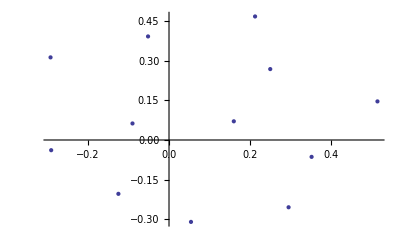

```mathematica
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,13},{j,2}]]]

p=Partition[mds[[2,All,-1]],2];
a=Table[Tooltip[p[[i]],statePostCode[[i]]],{i,1,statePostCode//Length}]

ListPlot[a]
```

```mathematica
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2+(x[i,3]-x[j,3])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,13},{j,3}]]]

p=Partition[mds[[2,All,-1]],3];
a=Table[Tooltip[Point[{p[[i,1]],p[[i,2]],p[[i,3]]}],statePostCode[[i]]],{i,1,statePostCode//Length}];


Graphics3D[a]
```

12.+(0.636971-√((x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2+(x[1,3]-x[2,3])^2))^2+(0.556277-√((x[1,1]-x[3,1])^2+(x[1,2]-x[3,2])^2+(x[1,3]-x[3,3])^2))^2+(0.510689-√((x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2+(x[2,3]-x[3,3])^2))^2+(0.618629-√((x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2+(x[1,3]-x[4,3])^2))^2+(0.540441-√((x[2,1]-x[4,1])^2+(x[2,2]-x[4,2])^2+(x[2,3]-x[4,3])^2))^2+(0.516605-√((x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2+(x[3,3]-x[4,3])^2))^2+(0.572632-√((x[1,1]-x[5,1])^2+(x[1,2]-x[5,2])^2+(x[1,3]-x[5,3])^2))^2+(0.492135-√((x[2,1]-x[5,1])^2+(x[2,2]-x[5,2])^2+(x[2,3]-x[5,3])^2))^2+(0.528302-√((x[3,1]-x[5,1])^2+(x[3,2]-x[5,2])^2+(x[3,3]-x[5,3])^2))^2+(0.588785-√((x[4,1]-x[5,1])^2+(x[4,2]-x[5,2])^2+(x[4,3]-x[5,3])^2))^2+(0.592751-√((x[1,1]-x[6,1])^2+(x[1,2]-x[6,2])^2+(x[1,3]-x[6,3])^2))^2+(0.56974-√((x[2,1]-x[6,1])^2+(x[2,2]-x[6,2])^2+(x[2,3]-x[6,3])^2))^2+(0.496536-√((x[3,1]-x[6,1])^2+(x[3,2]-x[6,2])^2+(x[3,3]-x[6,3])^2))^2+(0.559633-√((x[4,1]-x[6,1])^2+(x[4,2]-x[6,2])^2+(x[4,3]-x[6,3])^2))^2+(0.495575-√((x[5,1]-x[6,1])^2+(x[5,2]-x[6,2])^2+(x[5,3]-x[6,3])^2))^2+(0.557895-√((x[1,1]-x[7,1])^2+(x[1,2]-x[7,2])^2+(x[1,3]-x[7,3])^2))^2+(0.5-√((x[2,1]-x[7,1])^2+(x[2,2]-x[7,2])^2+(x[2,3]-x[7,3])^2))^2+(0.48037-√((x[3,1]-x[7,1])^2+(x[3,2]-x[7,2])^2+(x[3,3]-x[7,3])^2))^2+(0.561111-√((x[4,1]-x[7,1])^2+(x[4,2]-x[7,2])^2+(x[4,3]-x[7,3])^2))^2+(0.545035-√((x[5,1]-x[7,1])^2+(x[5,2]-x[7,2])^2+(x[5,3]-x[7,3])^2))^2+(0.552204-√((x[6,1]-x[7,1])^2+(x[6,2]-x[7,2])^2+(x[6,3]-x[7,3])^2))^2+(0.543788-√((x[1,1]-x[8,1])^2+(x[1,2]-x[8,2])^2+(x[1,3]-x[8,3])^2))^2+(0.473799-√((x[2,1]-x[8,1])^2+(x[2,2]-x[8,2])^2+(x[2,3]-x[8,3])^2))^2+(0.525463-√((x[3,1]-x[8,1])^2+(x[3,2]-x[8,2])^2+(x[3,3]-x[8,3])^2))^2+(0.582721-√((x[4,1]-x[8,1])^2+(x[4,2]-x[8,2])^2+(x[4,3]-x[8,3])^2))^2+(0.526667-√((x[5,1]-x[8,1])^2+(x[5,2]-x[8,2])^2+(x[5,3]-x[8,3])^2))^2+(0.526667-√((x[6,1]-x[8,1])^2+(x[6,2]-x[8,2])^2+(x[6,3]-x[8,3])^2))^2+(0.574074-√((x[7,1]-x[8,1])^2+(x[7,2]-x[8,2])^2+(x[7,3]-x[8,3])^2))^2+(0.554415-√((x[1,1]-x[9,1])^2+(x[1,2]-x[9,2])^2+(x[1,3]-x[9,3])^2))^2+(0.549425-√((x[2,1]-x[9,1])^2+(x[2,2]-x[9,2])^2+(x[2,3]-x[9,3])^2))^2+(0.481982-√((x[3,1]-x[9,1])^2+(x[3,2]-x[9,2])^2+(x[3,3]-x[9,3])^2))^2+(0.577982-√((x[4,1]-x[9,1])^2+(x[4,2]-x[9,2])^2+(x[4,3]-x[9,3])^2))^2+(0.462687-√((x[5,1]-x[9,1])^2+(x[5,2]-x[9,2])^2+(x[5,3]-x[9,3])^2))^2+(0.633333-√((x[6,1]-x[9,1])^2+(x[6,2]-x[9,2])^2+(x[6,3]-x[9,3])^2))^2+(0.485777-√((x[7,1]-x[9,1])^2+(x[7,2]-x[9,2])^2+(x[7,3]-x[9,3])^2))^2+(0.559284-√((x[8,1]-x[9,1])^2+(x[8,2]-x[9,2])^2+(x[8,3]-x[9,3])^2))^2+(0.578838-√((x[1,1]-x[10,1])^2+(x[1,2]-x[10,2])^2+(x[1,3]-x[10,3])^2))^2+(0.595294-√((x[2,1]-x[10,1])^2+(x[2,2]-x[10,2])^2+(x[2,3]-x[10,3])^2))^2+(0.497738-√((x[3,1]-x[10,1])^2+(x[3,2]-x[10,2])^2+(x[3,3]-x[10,3])^2))^2+(0.597043-√((x[4,1]-x[10,1])^2+(x[4,2]-x[10,2])^2+(x[4,3]-x[10,3])^2))^2+(0.471215-√((x[5,1]-x[10,1])^2+(x[5,2]-x[10,2])^2+(x[5,3]-x[10,3])^2))^2+(0.516484-√((x[6,1]-x[10,1])^2+(x[6,2]-x[10,2])^2+(x[6,3]-x[10,3])^2))^2+(0.465665-√((x[7,1]-x[10,1])^2+(x[7,2]-x[10,2])^2+(x[7,3]-x[10,3])^2))^2+(0.49467-√((x[8,1]-x[10,1])^2+(x[8,2]-x[10,2])^2+(x[8,3]-x[10,3])^2))^2+(0.598174-√((x[9,1]-x[10,1])^2+(x[9,2]-x[10,2])^2+(x[9,3]-x[10,3])^2))^2+(0.600877-√((x[1,1]-x[11,1])^2+(x[1,2]-x[11,2])^2+(x[1,3]-x[11,3])^2))^2+(0.578049-√((x[2,1]-x[11,1])^2+(x[2,2]-x[11,2])^2+(x[2,3]-x[11,3])^2))^2+(0.484706-√((x[3,1]-x[11,1])^2+(x[3,2]-x[11,2])^2+(x[3,3]-x[11,3])^2))^2+(0.53407-√((x[4,1]-x[11,1])^2+(x[4,2]-x[11,2])^2+(x[4,3]-x[11,3])^2))^2+(0.448352-√((x[5,1]-x[11,1])^2+(x[5,2]-x[11,2])^2+(x[5,3]-x[11,3])^2))^2+(0.49095-√((x[6,1]-x[11,1])^2+(x[6,2]-x[11,2])^2+(x[6,3]-x[11,3])^2))^2+(0.432967-√((x[7,1]-x[11,1])^2+(x[7,2]-x[11,2])^2+(x[7,3]-x[11,3])^2))^2+(0.447084-√((x[8,1]-x[11,1])^2+(x[8,2]-x[11,2])^2+(x[8,3]-x[11,3])^2))^2+(0.510158-√((x[9,1]-x[11,1])^2+(x[9,2]-x[11,2])^2+(x[9,3]-x[11,3])^2))^2+(0.57243-√((x[10,1]-x[11,1])^2+(x[10,2]-x[11,2])^2+(x[10,3]-x[11,3])^2))^2+(0.591966-√((x[1,1]-x[12,1])^2+(x[1,2]-x[12,2])^2+(x[1,3]-x[12,3])^2))^2+(0.576471-√((x[2,1]-x[12,1])^2+(x[2,2]-x[12,2])^2+(x[2,3]-x[12,3])^2))^2+(0.513889-√((x[3,1]-x[12,1])^2+(x[3,2]-x[12,2])^2+(x[3,3]-x[12,3])^2))^2+(0.585185-√((x[4,1]-x[12,1])^2+(x[4,2]-x[12,2])^2+(x[4,3]-x[12,3])^2))^2+(0.542986-√((x[5,1]-x[12,1])^2+(x[5,2]-x[12,2])^2+(x[5,3]-x[12,3])^2))^2+(0.512195-√((x[6,1]-x[12,1])^2+(x[6,2]-x[12,2])^2+(x[6,3]-x[12,3])^2))^2+(0.461039-√((x[7,1]-x[12,1])^2+(x[7,2]-x[12,2])^2+(x[7,3]-x[12,3])^2))^2+(0.519737-√((x[8,1]-x[12,1])^2+(x[8,2]-x[12,2])^2+(x[8,3]-x[12,3])^2))^2+(0.57631-√((x[9,1]-x[12,1])^2+(x[9,2]-x[12,2])^2+(x[9,3]-x[12,3])^2))^2+(0.60739-√((x[10,1]-x[12,1])^2+(x[10,2]-x[12,2])^2+(x[10,3]-x[12,3])^2))^2+(0.654229-√((x[11,1]-x[12,1])^2+(x[11,2]-x[12,2])^2+(x[11,3]-x[12,3])^2))^2

{12.9087,{x[1,1]→0.22053,x[1,2]→0.0830638,x[1,3]→-0.332124,x[2,1]→-0.292141,x[2,2]→-0.0503009,x[2,3]→0.190021,x[3,1]→-0.0364639,x[3,2]→-0.218963,x[3,3]→-0.313754,x[4,1]→-0.306441,x[4,2]→-0.370934,x[4,3]→0.0425004,x[5,1]→-0.456842,x[5,2]→0.021868,x[5,3]→-0.174015,x[6,1]→-0.370594,x[6,2]→-0.280252,x[6,3]→-0.334682,x[7,1]→0.0571212,x[7,2]→-0.0958374,x[7,3]→0.0502542,x[8,1]→-0.162037,x[8,2]→0.232867,x[8,3]→-0.316995,x[9,1]→0.0297431,x[9,2]→0.196052,x[9,3]→0.0639258,x[10,1]→-0.21688,x[10,2]→-0.0265644,x[10,3]→-0.519536,x[11,1]→-0.313957,x[11,2]→0.221923,x[11,3]→-0.068013,x[12,1]→0.105215,x[12,2]→-0.362151,x[12,3]→-0.106649,x[13,1]→-0.392469,x[13,2]→-0.137372,x[13,3]→0.0101592}}

-Graphics3D-